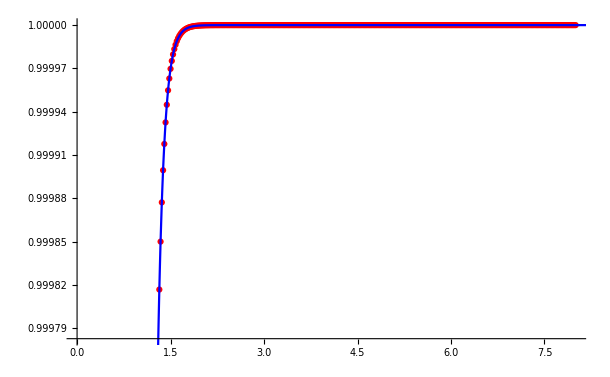

```mathematica
logisticIC = 0.01;
logisticExact[t_] := 0.01/(0.01+0.99*E^(-10t));
errorListPlot[approx_] := (
ListPLot[Table[{approx[[i,1]],Abs[logisticExact[approx[[i,1]]]-approx[[i,2]]]}, {i,1,Length[approx]}]]
);

f[t_,u_] := 10*u*(1-u);

RK4[f_,y0_,h_,T_] := (
Block[{y,t,n,i,k1,k2,k3,k4},
n = T/h;
t= Table[i*h,{i,0,n}];
y = Table[0,n+1];
y[[1]]=y0;
For[i=1, i<=n,++i,
k1 = h f[t[[i]],y[[i]]];
k2 = h f[t[[i]]+0.5h,y[[i]]+0.5*k1];
k3 = h f[t[[i]]+0.5h,y[[i]]+0.5*k2];
k4 = h f[t[[i]]+h,y[[i]]+k3];
y[[i+1]]=y[[i]]+((1/6)k1+(1/3) k2 + (1/3) k3+(1/6) k4);
];
Return[Table[{t[[i]],y[[i]]},{i,1,n+1}]];
]
)

res = RK4[f,0.01,0.02,8];
plot1 = ListPlot[res,PlotStyle->Red];
plot2 = Plot[logisticExact[t],{t,-1,10},PlotStyle->Blue];
Show[{plot1,plot2}]
```